```mathematica
ListSigmaOfΣn[Σn_]:=Join[Σn/@domain[Σn],ListComplement[ListSigmaAll,Σn/@domain[Σn]]]
```

```mathematica
ListSigmaOfΣn[ΣnTETXISO]
ListSigmaOfΣn[ΣnTETCUBE]
```

```mathematica
SigmaPairsMatrix[Σn_,dim_]:=Table[{Take[ListSigmaOfΣn[Σn],dim][[j]],Take[ListSigmaOfΣn[Σn],dim][[k]]},{j,dim},{k,dim}];
```

#### Example

```mathematica
MatrixForm[SigmaPairsMatrix[ΣnTETCUBE,6]]
```

#### Here is how the Map function works .

```mathematica
MatrixForm[Map[#[[1]]+#[[2]]&,SigmaPairsMatrix[ΣnTETCUBE,6],{2}]]
```

```mathematica
InternodalAngles[Tmat_,Σn_,nm_,dim_]:=Map[Round[AngleMatrix[SmatOfΣ[#[[1]],Tmat,Σn,nm],SmatOfΣ[#[[2]],Tmat,Σn,nm]]/Degree,.01]&,SigmaPairsMatrix[Σn,dim],{2}];
```

#### Examples

```mathematica
nm=nm2;Σn=ΣnTETXISO;
MatrixNote[Tmat]
TextNodeMode[nm]
ListSigmaOfΣn[Σn]
MatrixForm[InternodalAngles[Tmat,Σn,nm,6]]
MatrixForm[InternodalAngles[Tmat,Σn,nm,8]]
```

```mathematica
rrow[i_,Tmat_,Σn_,nm_,dim_]:=Join[{Take[ListSigmaOfΣn[Σn],dim][[i]]},InternodalAngles[Tmat,Σn,nm,dim][[i]]];
rrow[0,Tmat_,Σn_,nm_,dim_]:=Join[{""},Take[ListSigmaOfΣn[Σn],dim]];
```

#### Examples

```mathematica
Σn=ΣnTETCUBE;dim=8;
rrow[0,Tmat,Σn,nm2,dim]
rrow[3,Tmat,Σn,nm2,dim]
```

```mathematica
dim=6;WantNumbers="WantNumbers";
MatrixNote[Tmat]
TextNodeMode[nm]
MatrixForm[Table[rrow[i,Tmat,Σn,nm,dim],{i,0,dim}]]
```

```mathematica
gg[i_,j_,Tmat_,Σn_,nm_,dim_]:=InternodalAngles[Tmat,Σn,nm,dim][[i,j]];
```

#### Example

```mathematica
MatrixNote[Tmat]
TextNodeMode[nm]
gg[4,5,Tmat,ΣnTETXISO,nm,6]
```

```mathematica
Sort[Flatten[InternodalAngles[Tmat,Σn,nm,8]]]
```

```mathematica
ForScaling:=Max[Flatten[InternodalAngles[Tmat,ΣnTETXISO,nm2,8]]]; (* May need to change *)
```

```mathematica
ForScaling
```

```mathematica
PreCheckerboard[Tmat_,Σn_,nm_,dim_,ForScaling_,WantNumbers_]:={Table[{FaceForm[ColorData["TemperatureMap"][gg[i,j,Tmat,Σn,nm,dim]/ForScaling]],Cuboid[{i-.5,-j-.5},{i+.5,-j+.5}]},{i,dim},{j,dim}],
If[WantNumbers=="WantNumbers",Table[Text[Style[Round[gg[i,j,Tmat,Σn,nm,dim],.1],13],{i,-j}],{i,dim},{j,dim}]]};
```

```mathematica
hw=1.5;fontsize=15;WantRound="NoWantRound";increment=2;offset=2.5;
Show[legends[Range[0,24,4],22,SubscriptBox[Style["α",20],Style["MONO",11]]//DisplayForm,hw,fontsize,increment,offset],ImageSize->100,PlotRange->All]
```

```mathematica
Checkerboard[Tmat_,Σn_,nm_,dim_,ForScaling_,WantNumbers_,WantLegends_]:=Graphics[{
Text[#,{Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]],0}]&/@Take[ListSigmaOfΣn[Σn],dim],
Text[#,{-.2,-Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]]}]&/@Take[ListSigmaOfΣn[Σn],dim],PreCheckerboard[Tmat,Σn,nm,dim,ForScaling,WantNumbers],
If[WantLegends=="WantLegends",Inset[legends[Range[0,5+ForScaling,5],ForScaling,"",hww,fontsize,increment,offset],{3+dim,-3},Center,1.8] ]},ImageSize->If[WantLegends=="WantLegends",510,350]](* legends *)
```

```mathematica
nm=nm4;Σn=ΣnTETXISO;dim=6;WantNumbers="WantNumbers"
PreCheckerboard[Tmat,Σn,nm,dim,ForScaling,WantNumbers]
```

#### Examples

```mathematica
ForScaling
```

#### For legends. The setting increment = n prints every n^th contour label.

```mathematica
hww=1.2;fontsize=12;increment=1;offset=2.5; WantRound=="NoWantRound";
```

```mathematica
nm=nm4;Σn=ΣnTETXISO;dim=6;
MatrixNote[Tmat]
TextNodeMode[nm]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","NoWantLegends"]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","WantLegends"]
Print[" "];
```

```mathematica
nm=nm2;Σn=ΣnTETCUBE;dim=8;
MatrixNote[Tmat]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","NoWantLegends"]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","WantLegends"]
Print[" "];
nm=nm3;Σn=ΣnTETXISO;dim=6;  (* dim must be nMax[Σn] for nm3 *)
MatrixNote[Tmat]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"WantNumbers","NoWantLegends"]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"WantNumbers","WantLegends"]
Print[" "];
```

```mathematica
dim=6;
MatrixNote[Tmat]
Print[" UforNM4 = ", MatrixForm[UforNM4]];
Row[{Checkerboard[Tmat,ΣnTETXISO,nm2,dim,ForScaling,"WantNumbers","noWantLegends"],
Checkerboard[Tmat,ΣnTETXISO,nm3,dim,ForScaling,"WantNumbers","noWantLegends"],
Checkerboard[Tmat,ΣnTETXISO,nm4,dim,ForScaling,"WantNumbers","WantLegends"]}]
```

## Archive

T is Brown

UforNM4 = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

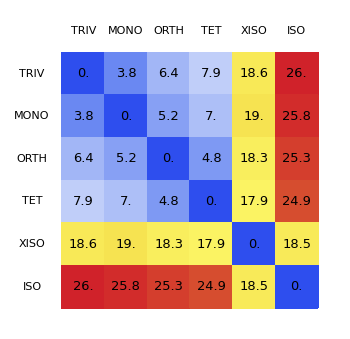
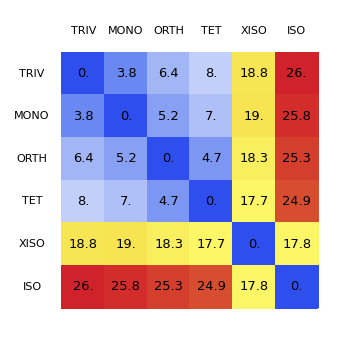
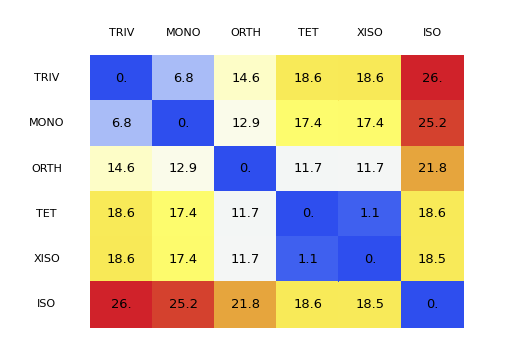
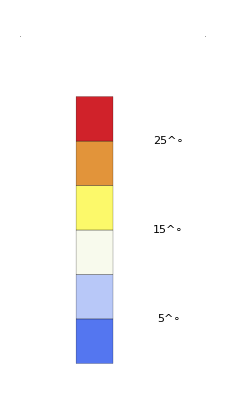

T is Igel

UforNM4 = (0.0498003 | -0.997825 | 0.0431815
0.753887 | 0.0659144 | 0.65369
-0.655115 | 0. | 0.75553)

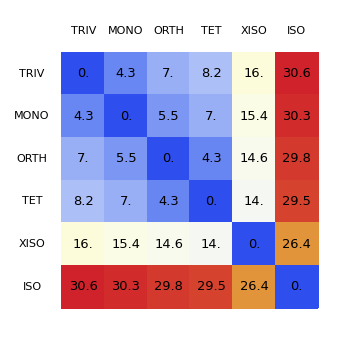
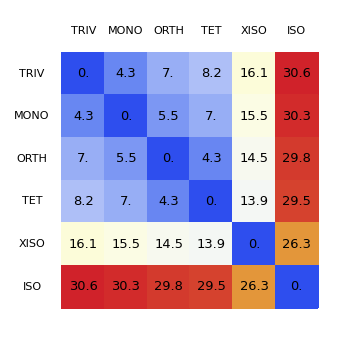
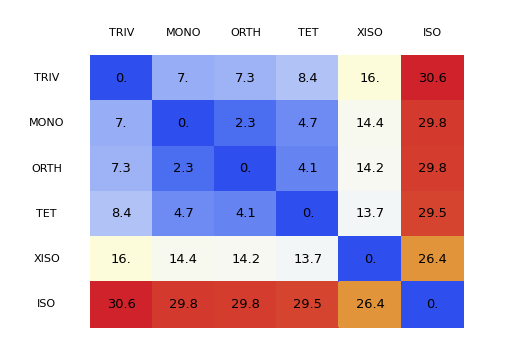
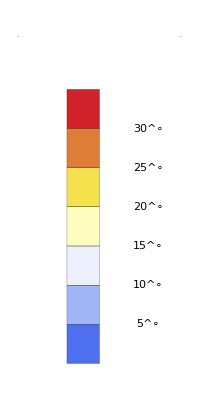

T is SSA2023

UforNM4 = (0.116812 | -0.955654 | 0.270334
0.379065 | 0.294492 | 0.87726
-0.917968 | 0. | 0.396655)

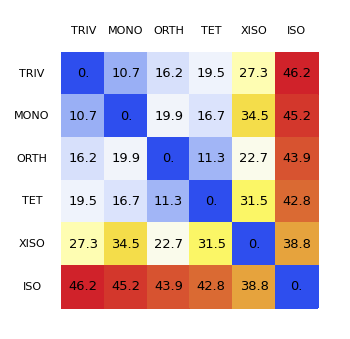
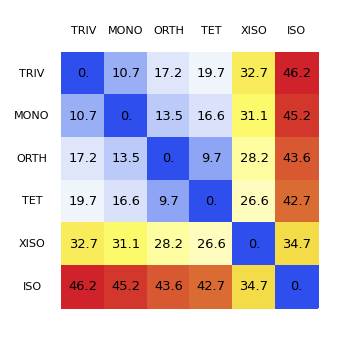
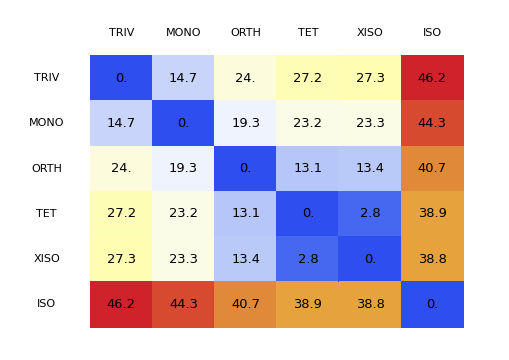
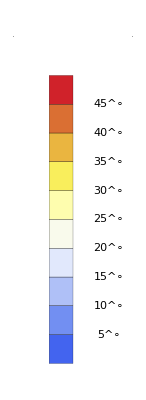

T is Mar17

UforNM4 = (0.261187 | -0.95316 | 0.152536
0.823076 | 0.302466 | 0.480686
-0.504308 | 0. | 0.863524)